# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["/Users/pcs/Desktop/Entropy/Late time distributions/QMB.wl"];
```

MessageName::messg: TranslationEigenvectorRepresentatives::usage cannot be set to FormatUsage[TranslationEigenvectorRepresentatives[L] returns a list of sublists, each containing:  the decimal representation of a bit-string representative eigenvector,  its pseudomomentum k, and the length of its translation orbit,  for a system of ```L``` qubits.]. It must be set to a string.

MessageName::messg: BlockDiagonalize::usage cannot be set to FormatUsage[BlockDiagonalize[matrix,opts] returns ```matrix``` in block-diagonal form. Only 	option is '''Symmetry'''.]. It must be set to a string.

MessageName::messg: Transform::usage cannot be set to FormatUsage[Matrix transform for Translation symmetry]. It must be set to a string.

General::stop: Further output of MessageName::messg will be suppressed during this calculation.

```mathematica
LaunchKernels[8]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]]+I RandomVariate[NormalDistribution[0,1]],{2^L}]];
(*haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]],{2^L}]];*)
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
Clear[rhoa];
rhoa[ini_,t_,L_,k_,val_,vec_]:=Module[{M,rhoc,rhob,rho,ck=Conjugate[vec] . ini,phases=arrayt[t,val,vec],perm=Delete[Range[L],{k}]},
MatrixPartialTrace[Dyad[N[Total[phases*ck]]],perm,2]
];
(*Clear[new];
new[ini_,t_,L_,k_,val_,vec_]:=Module[{ope=Pauli[3],rho=rhoa[ini,t,L,k,val,vec]},
Total[Map[VNentropy,(Chop[Eigenvalues[rho]])]]
];*)
Clear[sdiagonal];
sdiagonal[ini_,L_,k_]:=Module[{rho=Dyad[ini],perm=Delete[Range[L],{k}],rhoa},
rhoa=MatrixPartialTrace[Dyad[ini],perm,2];
Total[Map[VNentropy,(Chop[Eigenvalues[rhoa]])]]
];
Clear[rhoa];
rhoa[ini_,t_,L_,k_,val_,vec_]:=Module[{M,rhoc,rhob,rho,ck=Conjugate[vec] . ini,phases=arrayt[t,val,vec],perm=Delete[Range[L],{k}]},
MatrixPartialTrace[Dyad[N[Total[phases*ck]]],perm,2]
];
Clear[mag];
mag[L_,k_,ini_,t_,val_,vec_]:=Module[{ope=Pauli[3],rho=rhoa[ini,t,L,k,val,vec]},
Chop[Tr[rho.ope]]
];
Clear[vnentropy];
vnentropy[L_,k_,ini_,t_,val_,vec_]:=Module[{rho=rhoa[ini,t,L,k,val,vec]},
Total[Map[VNentropy,(Chop[Eigenvalues[rho]])]]
];
Clear[ClusterByWindow];
ClusterByWindow[energies_List,window_]:=Module[{e,s=Sort[energies],clusters={},curr,mn,mx},If[s==={},Return[{}]];
curr={First[s]};mn=mx=First[s];
Do[e=x;
If[Max[mx,e]-Min[mn,e]<=window,AppendTo[curr,e];mn=Min[mn,e];mx=Max[mx,e],AppendTo[clusters,curr];curr={e};mn=mx=e],{x,Rest[s]}];
AppendTo[clusters,curr];
clusters];

Clear[arrayt];
arrayt[t_,val_,vec_]:=Exp[-I*val*t]*vec;
Clear[new];
new[L_,eigenval_,eigenvec_,ini_,t_]:=Module[{schmidt,psit,ck=Conjugate[eigenvec].ini,d=2^(L/2),phases=arrayt[t,eigenval,eigenvec]},
psit=ArrayReshape[Total[N[ck*phases]],{d,d}];
Total[Map[VNentropy,(Chop[SingularValueList[psit]])^2]]];
Clear[sur];
sur[eigenval_,eigenvec_,ini_,t_]:=Module[{psit,phases=arrayt[t,eigenval,eigenvec],ck=Conjugate[eigenvec].ini},
Abs[Conjugate[Total[N[ck*phases]]].ini]^2
];
Clear[ExpandBlockVector];
ExpandBlockVector[v_,map_,type_,L_]:=Module[{full=ConstantArray[0,2^L],k=1,a,b,coeff},
Do[
If[Length[pair]==1,full[[pair[[1]]+1]]=v[[k]],{a,b}=pair;
coeff=v[[k]]/Sqrt[2];
If[type=="even",full[[a+1]]=coeff;full[[b+1]]=coeff,full[[a+1]]=coeff;full[[b+1]]=-coeff];];
k++,{pair,map}];
full];
Clear[revIndex];
revIndex[i_,L_]:=FromDigits[Reverse[IntegerDigits[i,2,L]],2];

Unfold[eigenvalues_List] := 
Module[
	{skd, unfolded, n, smoothCDF, smoothPDF},
	
	n=Length[eigenvalues];
	
	(*Create smooth kernel distribution for the CDF*)
	skd=SmoothKernelDistribution[eigenvalues, "StandardGaussian", {
		"Bounded", {Min[eigenvalues], Max[eigenvalues]}, "Gaussian"
		}];
		
	(*Unfold:ε_i=N*CDF(E_i)*)
	unfolded = Table[ n*CDF[skd, eigenvalues[[i]]], {i,n}];
	
	(*Define the smooth functions*)
	smoothCDF=Function[x,n*CDF[skd,x]];
	smoothPDF=Function[x,n*PDF[skd,x]];
	
	(*Return unfolded spectrum and related functions*)
	<|"UnfoldedLevels"->unfolded,
	"SmoothCDF"->smoothCDF,(*Cumulative:N(E)*)
	"SmoothPDF"->smoothPDF,(*Density:ρ(E)*)
	"Bandwidth"->skd["Bandwidth"],
	"OriginalLevels"->eigenvalues(*Useful for comparison*)|>
]
```

# Parallelization mix estrategies (strat 4&5)

```mathematica
J=1;
h=1;
```

```mathematica
L=14;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
Clear[ProjectBlockVector];
ProjectBlockVector[state_,map_,type_,L_]:=Module[{res,k=1,a,b},res=ConstantArray[0,Length[map]];
Do[If[Length[pair]==1,res[[k]]=state[[pair[[1]]+1]],{a,b}=pair;
If[type=="even",res[[k]]=(state[[a+1]]+state[[b+1]])/Sqrt[2],res[[k]]=(state[[a+1]]-state[[b+1]])/Sqrt[2]];];
k++,{pair,map}];
res];
Clear[ExpandFullState];
ExpandFullState[evenState_,oddState_,evenMap_,oddMap_,L_]:=ExpandBlockVector[evenState,evenMap,"even",L]+ExpandBlockVector[oddState,oddMap,"odd",L];
(*---Define helper to build expansion matrices---*)
Clear[makeExpansionMatrix];
makeExpansionMatrix[map_,L_,type_]:=SparseArray[Flatten[Table[If[Length[pair]==1,{{pair[[1]]+1,k}->1},Which[type==="even",{{pair[[1]]+1,k}->1/Sqrt[2],{pair[[2]]+1,k}->1/Sqrt[2]},type==="odd",{{pair[[1]]+1,k}->1/Sqrt[2],{pair[[2]]+1,k}->-1/Sqrt[2]}]],{k,Length[map]},{pair,{map[[k]]}}],2],{2^L,Length[map]}];
(*---Define the pure (uncompiled) fast expander---*)
Clear[expandFullStateFastTemplate];
expandFullStateFastTemplate[evenMat_,oddMat_][evenState_,oddState_]:=evenMat.evenState+oddMat.oddState;
(*---1. Define your helper functions---*)
Clear[new];
new[colVec_,L_]:=Module[{M,s,p},M=ArrayReshape[colVec,{2^(L/2),2^(L/2)}];
Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]];
Clear[compiledEvolverSector];
compiledEvolverSector[eigenvec_,eigenval_]:=With[{evT=Transpose[eigenvec],evC=Conjugate[eigenvec]},
Compile[{{state,_Complex,1},{tlist,_Real,1}},
Module[{ck,evolvedCoeffs},
ck=evC.state;
Table[evT.(ck*Exp[-I*eigenval*t]),{t,tlist}]],
CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}]];
```

```mathematica
g=0.05;
```

```mathematica
Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
```

```mathematica
(*pack for performance*)
evenEigenvec=Developer`ToPackedArray[eveneigenvec];
evenEigenval=Developer`ToPackedArray[eveneigenval];
oddEigenvec=Developer`ToPackedArray[oddeigenvec];
oddEigenval=Developer`ToPackedArray[oddeigenval];
```

```mathematica
(*---2. Define parameters and data (on master only)---*)
tlist=Table[10^i,{i,-1,4,0.01}];
tlist=Developer`ToPackedArray[tlist];
tlist//Length
```

501

```mathematica
(*---3. Send only lightweight definitions to subkernels---*)
DistributeDefinitions[compiledEvolverSector,new,L,RandomChainProductState,ExpandFullState,ProjectBlockVector,evenMap,oddMap,makeExpansionMatrix,expandFullStateFastTemplate];
```

```mathematica
ParallelEvaluate[
(evenExpansionMatrix=makeExpansionMatrix[evenMap,L,"even"];
oddExpansionMatrix=makeExpansionMatrix[oddMap,L,"odd"];
ExpandFullStateFast=Compile[{{evenState,_Complex,1},{oddState,_Complex,1}},expandFullStateFastTemplate[evenExpansionMatrix,oddExpansionMatrix][evenState,oddState],CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}];)
];
```

```mathematica
(*---4. Build heavy objects ONCE per kernel---*)
ParallelEvaluate[
(eveneigenveclocal=evenEigenvec;
eveneigenvallocal=evenEigenval;
oddeigenveclocal=oddEigenvec;
oddeigenvallocal=oddEigenval;
tlistLocal=tlist;

evenEvolver=compiledEvolverSector[evenEigenvec,evenEigenval];
oddEvolver=compiledEvolverSector[oddEigenvec,oddEigenval];

entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenfinal,oddfinal,final},
{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenfinal=evenEvolver[psiEven,tlistLocal];
oddfinal=oddEvolver[psiOdd,tlistLocal];
final=Table[ExpandFullStateFast[evenfinal[[i]],oddfinal[[i]]],{i,Length[tlistLocal]}];
Map[new[#,L]&,final]];
)];
```

```mathematica
(*---6. Parallel computation (efficient+no data duplication)---*)
```

```mathematica
AbsoluteTiming[data=ParallelTable[Module[{state=RandomChainProductState[L]},entanglementWorker[state]],{200}];]
```

{8363.76,Null}

```mathematica
8363/60.
```

139.383

```mathematica
139/60.
```

2.31667

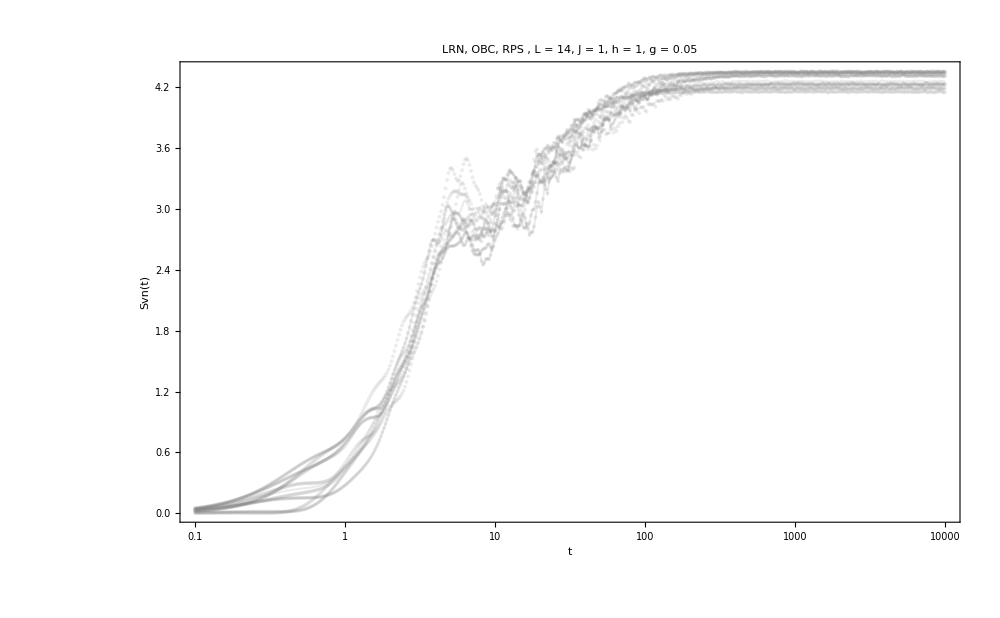

```mathematica
plot1=ListLogLinearPlot[Table[Transpose[{tlist,i}],{i,data[[1;;-1;;20]]}],PlotStyle->{Directive[Gray,Opacity[0.15]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

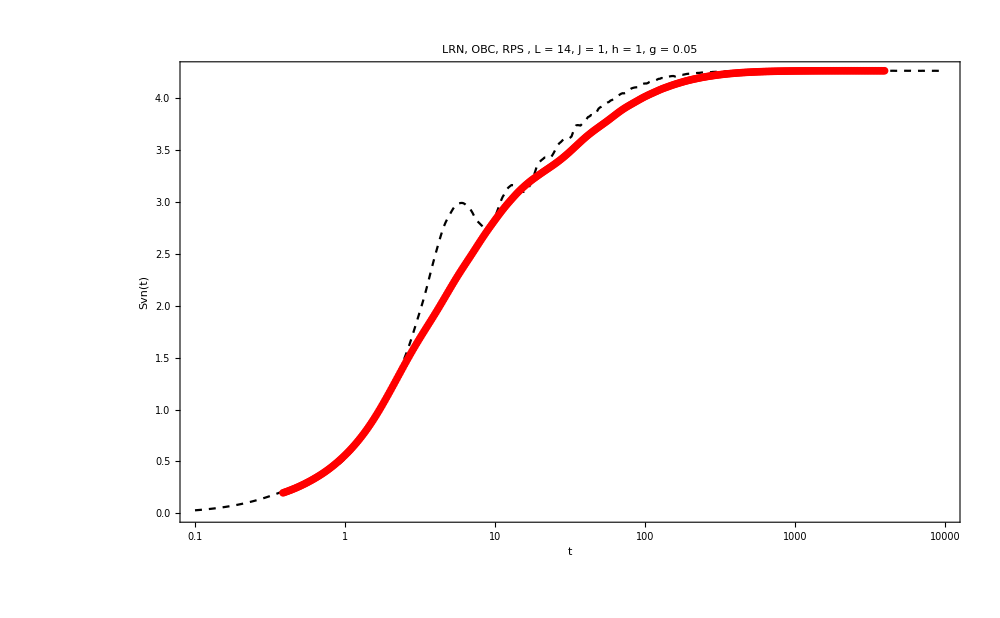

```mathematica
plot2=ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],100]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Red,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

```mathematica
finalrps=Table[i[[-1]],{i,data}];
{bins,heights}=HistogramList[finalrps,"FreedmanDiaconis","Probability"];
ymax=1.01*Max[heights];   (*5% taller than tallest bin*)
```

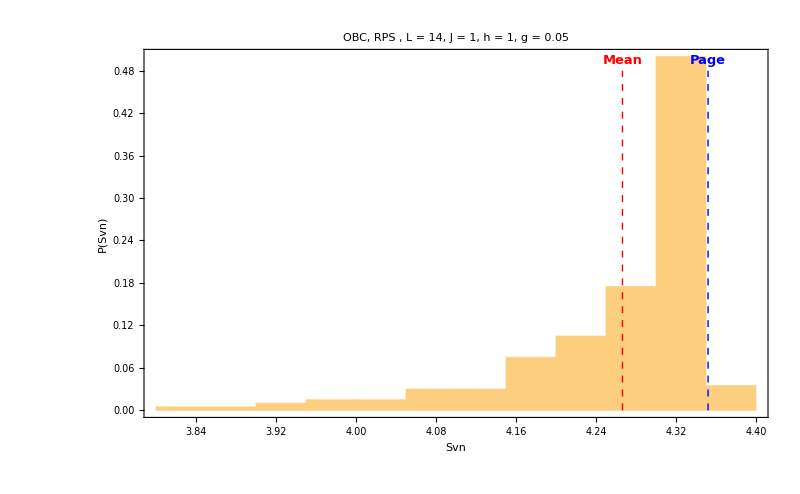

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalrps],0},{Mean[finalrps],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalrps],ymax*0.98},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*0.98},{-1,0}]},PlotRange->All]
```